```mathematica
Clear[ρ0]
ρ0[m_Integer,i_Integer]/;0≤i≤Floor[(m-2)/2]:=ρ0[m,i]=With[{λ=(-1)^(m-i)qi[i] qi[m]^-1},
SparseArray[{Band[{1,2}]->1,Band[{m-2i,1}]->1},{m-2i,m-2i}]+SparseArray[{Band[{2,1}]->λ,Band[{1,m-2i}]->λ},{m-2i,m-2i}]
]
```

```mathematica
ρ0[4,0]//Normal//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

```mathematica
Eigenvalues[ρ0[10,0]]
```

{-(-1)^(2/5),(-1)^(2/5),-(-1)^(1/5),(-1)^(1/5),(-1)^(3/5),-(-1)^(3/5),(-1)^(4/5),-(-1)^(4/5),-1,1}

```mathematica
ρ0[6,1]//Normal//MatrixForm
```

(0 | 1 | 0 | -qi[1]/qi[6]
-qi[1]/qi[6] | 0 | 1 | 0
0 | -qi[1]/qi[6] | 0 | 1
1 | 0 | -qi[1]/qi[6] | 0)

```mathematica
Eigenvalues[ρ0[6,1]]
```

{(qi[1]-qi[6])/qi[6],(-qi[1]+qi[6])/qi[6],-(ⅈ (qi[1]+qi[6]))/qi[6],(ⅈ (qi[1]+qi[6]))/qi[6]}

```mathematica
Eigenvalues[ρ0[8,0]]
```

{-1,ⅈ,-ⅈ,1,-(-1)^(1/4),(-1)^(1/4),(-1)^(3/4),-(-1)^(3/4)}

```mathematica
Eigenvalues[ρ0[8,1]]
```

{(qi[1]-qi[8])/qi[8],(-qi[1]+qi[8])/qi[8],(qi[1]-qi[8]-√3 √(-qi[1]^2-2 qi[1] qi[8]-qi[8]^2))/(2 qi[8]),(-qi[1]+qi[8]-√3 √(-qi[1]^2-2 qi[1] qi[8]-qi[8]^2))/(2 qi[8]),(qi[1]-qi[8]+√3 √(-qi[1]^2-2 qi[1] qi[8]-qi[8]^2))/(2 qi[8]),(-qi[1]+qi[8]+√3 √(-qi[1]^2-2 qi[1] qi[8]-qi[8]^2))/(2 qi[8])}

```mathematica
Eigenvalues[ρ0[8,2]]
```

{(-qi[2]-qi[8])/qi[8],-(ⅈ (qi[2]-qi[8]))/qi[8],(ⅈ (qi[2]-qi[8]))/qi[8],(qi[2]+qi[8])/qi[8]}

```mathematica
ρ0[8,0]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ρ0[8,1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | -qi[1]/qi[8]
-qi[1]/qi[8] | 0 | 1 | 0 | 0 | 0
0 | -qi[1]/qi[8] | 0 | 1 | 0 | 0
0 | 0 | -qi[1]/qi[8] | 0 | 1 | 0
0 | 0 | 0 | -qi[1]/qi[8] | 0 | 1
1 | 0 | 0 | 0 | -qi[1]/qi[8] | 0)

```mathematica
ρ0[8,2]//MatrixForm
```

(0 | 1 | 0 | qi[2]/qi[8]
qi[2]/qi[8] | 0 | 1 | 0
0 | qi[2]/qi[8] | 0 | 1
1 | 0 | qi[2]/qi[8] | 0)

```mathematica
ρ0[8,3]//MatrixForm
```

(0 | 1-qi[3]/qi[8]
1-qi[3]/qi[8] | 0)

```mathematica
Eigenvalues[ρ0[8,3]]
```

{-1+qi[3]/qi[8],1-qi[3]/qi[8]}

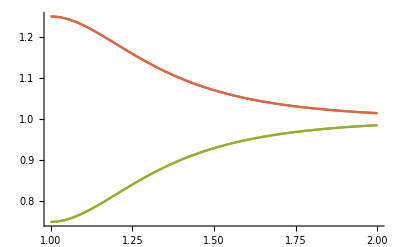

```mathematica
Plot[Evaluate[Abs[Eigenvalues[ρ0[8,2]]/.qi[k_]:>(q^k-q^-k)/(q-q^-1)]],{q,1,2}]
```

```mathematica
Abs[%]
```

{0.886166,0.886166,1.0615,1.0615,1.0615,1.0615}

```mathematica
e[m_,i_]:=Table[(-1)^(m-i)qi[i]/qi[m] Exp[2π ⅈ r/(m-2i)]+Exp[-2π ⅈ r/(m-2i)],{r,0,m-2i-1}]
```

```mathematica
e[8,2]
```

{1+qi[2]/qi[8],-ⅈ+(ⅈ qi[2])/qi[8],-1-qi[2]/qi[8],ⅈ-(ⅈ qi[2])/qi[8]}

```mathematica
e[8,3]/.qi[k_]:>(q^k-q^-k)/(q-q^-1)
```

{1-(-1/q^3+q^3)/(-1/q^8+q^8),-1+(-1/q^3+q^3)/(-1/q^8+q^8)}

```mathematica
c[z_]:={Re[z],Im[z]}
```

```mathematica
circle=ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π}];
```

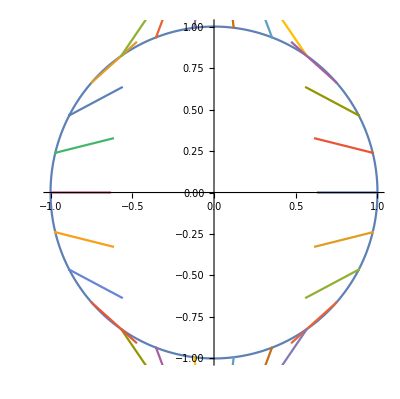

```mathematica
Show[{circle,ParametricPlot[Evaluate[c/@(e[100,37]/.qi[k_]:>(q^k-q^-k)/(q-q^-1))],{q,1+10.^-6,2}]}]
```

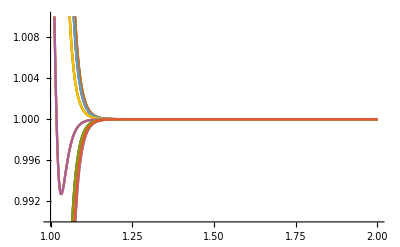

```mathematica
Plot[Evaluate[Abs[e[100,37]/.qi[k_]:>(q^k-q^-k)/(q-q^-1)]],{q,1+10.^-6,2},PlotRange->{0.99,1.01}]
```

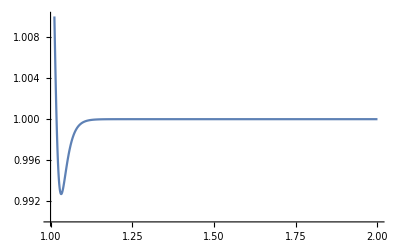

```mathematica
Plot[Evaluate[Abs[e[100,37]⟦4⟧/.qi[k_]:>(q^k-q^-k)/(q-q^-1)]],{q,1+10.^-6,2},PlotRange->{0.99,1.01}]
```

```mathematica
Let's look for triples (m,i,r)
```

```mathematica
rs[m_,i_]:=Cases[Range[0,m-2i-1],r_/;Mod[3r m,m-2i]==0]
```

```mathematica
rs[100,2]
```

{0,8,16,24,32,40,48,56,64,72,80,88}

```mathematica
qi[2]^2/.qi[k_]:>(q^k-q^-k)/(q-q^-1)/.q->(1+√5)/2//N
```

5.

```mathematica
Solve[(qi[2]^2/.qi[k_]:>(q^k-q^-k)/(q-q^-1))==5.25]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q→-1.70466},{q→-0.586627},{q→0.586627},{q→1.70466}}

```mathematica
Clear[rs];
rs[m_,i_]:=rs[m,i]=Cases[Range[0,m-2i-1],r_/;Mod[3r m,m-2i]==0∧0<(-1)^(m-i+1)2Cos[(2π r)/(m-2i)]<(qi[i]/qi[m]/.qi[k_]:>(q^k-q^-k)/(q-q^-1)/.q->(1+√5)/2)]
```

```mathematica
Dynamic[m]
```

```mathematica
Do[Print/@DeleteCases[Table[{m,i,rs[m,i]},{i,0,(m-2)/2}],{_,_,{}}],{m,2,10000,2}]
```